```mathematica
θs={1,0.1,0.01,0.001,0};
Subscript[M, pl]=1.22 10^22;
m=100;
g=10.75;
Tmax=300;
Tmin=0.2;
τ=1; (*sec*)
Γ=τ^-1 6.58 10^-22;
H[T_]:=√((8 π^3 g)/90)T^2/Subscript[M, pl];
t[T_]:=1/(2H[T]);
s[T_]:=(2 π^2)/45 g T^3;
Subscript[n, eq][T_]:=NIntegrate[p^2/(Exp[(√(p^2+m^2))/T]+1),{p,0,∞}];

Off[NIntegrate::inumr];
(*On[NIntegrate::inumr];*)
```

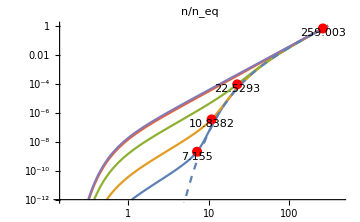
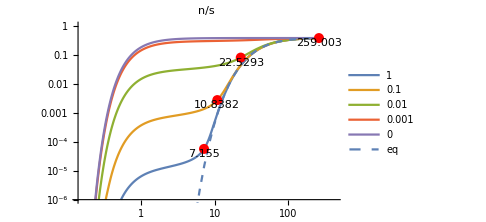

```mathematica
σ[θ_]:=(5 θ^2)/(2π)(3 10^5)^-4 m^2;
sol[θ_:10^-2]:=(Subscript[n, N][T]/.First[NDSolve[{
D[Subscript[n, N][T], T]/D[t[T], T]+3H[T] Subscript[n, N][T]==-σ[θ]((Subscript[n, N][T])^2-(Subscript[n, eq][T])^2)-Γ Subscript[n, N][T],
Subscript[n, N][Tmax]==Subscript[n, eq][Tmax]
},Subscript[n, N],{T,Tmax,Tmin}]]);

Quiet[Module[{Ts},(
(Ts[#]=(FindRoot[H[T]==σ[#]Subscript[n, eq][T],{T,Tmax}]//Values//Max))&/@θs;
HΓpointsNeq=Select[
With[{p={Log[Ts[#]],Log[sol[#]/Subscript[n, eq][Tmax]/.T-> Ts[#]]}},{Red,Point[p],Black,Text[Ts[#],p,{0,1}]}]&/@θs,Tmin≤#⟦4,1⟧≤Tmax&];
HΓpointsS=Select[
With[{p={Log[Ts[#]],Log[sol[#]/s[T]/.T-> Ts[#]]}},{Red,Point[p],Black,Text[Ts[#],p,{0,1}]}]&/@θs,Tmin≤#⟦4,1⟧≤Tmax&];
)]];

Row[{
Show[{
LogLogPlot[Evaluate[sol[#]/Subscript[n, eq][Tmax]&/@θs],{T,Tmin,Tmax},PlotRange->{10^-12,1},PlotLabel->"n/n_eq",Epilog->Flatten[{PointSize[0.02],HΓpointsNeq}],ImageSize->Medium],
LogLogPlot[Subscript[n, eq][T]/Subscript[n, eq][Tmax],{T,Tmin,Tmax},PlotStyle->Dashed]
}],
Show[{
LogLogPlot[Evaluate[sol[#]/s[T]&/@θs],{T,Tmin,Tmax},PlotLegends->θs,PlotRange->{10^-6,1},PlotLabel->"n/s",Epilog->Flatten[{PointSize[0.02],HΓpointsS}],ImageSize->Medium],
LogLogPlot[Subscript[n, eq][T]/s[T],{T,Tmin,Tmax},PlotLegends->{"eq"},PlotStyle->Dashed]
}]
}]
```